Part::partd: Part specification {a,b}⟦1,1⟧ is longer than depth of object.

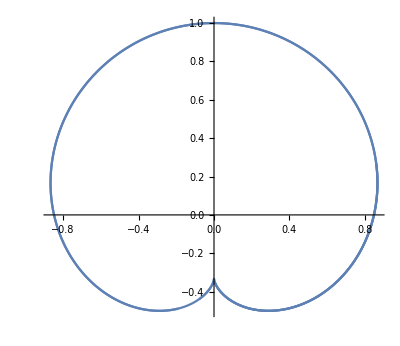

```mathematica
F[x_,y_,t_]:=(Cos[2^(1-Floor[Log[t]]) π t]-Cos[2^(3-Floor[Log[4 t]]) π t]) x+(Sin[2^(1-Floor[Log[t]]) π t]-Sin[2^(3-Floor[Log[4 t]]) π t])y-Sin[2 (2^(-Floor[Log[t]])-2^(2-Floor[Log[4 t]])) π t];
Fd[x_,y_,t_]:= -2^(-Floor[Log[t]]) (Cos[2 (2^(-Floor[Log[t]])-2^(2-Floor[Log[4 t]])) π t]-Cos[2^(1-Floor[Log[t]]) π t] y+x Sin[2^(1-Floor[Log[t]]) π t])+2^(2-Floor[Log[4 t]]) (Cos[2 (2^(-Floor[Log[t]])-2^(2-Floor[Log[4 t]])) π t]-Cos[2^(3-Floor[Log[4 t]]) π t] y+x Sin[2^(3-Floor[Log[4 t]]) π t]);
parametricF[t_]:=(
Solve[F[a,b,t]==0&&Fd[a,b,t]==0,{a,b}]);
pFx[t_]:=({a,b}/.parametricF[t])[[1,1]];
pFy[t_]:=({a,b}/.parametricF[t])[[1,2]];
ParametricPlot[{pFx[t],pFy[t]},{t,0,2}]
```

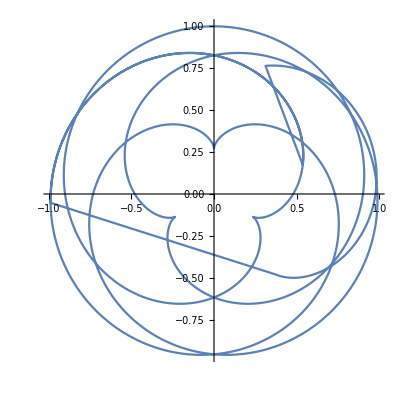

```mathematica
F[x_,y_,t_]:=(Cos[2^(1-Floor[Log[t]]) π t]-Cos[7 2^(1-Floor[Log[7 t]]) π t]) x+(Sin[2^(1-Floor[Log[t]]) π t]-Sin[7 2^(1-Floor[Log[7 t]]) π t])y-Sin[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t];
Fd[x_,y_,t_]:= -2^(-Floor[Log[t]]) (Cos[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t]-Cos[2^(1-Floor[Log[t]]) π t] y+x Sin[2^(1-Floor[Log[t]]) π t])+7 2^(-Floor[Log[7 t]]) (Cos[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t]-Cos[7 2^(1-Floor[Log[7 t]]) π t] y+x Sin[7 2^(1-Floor[Log[7 t]]) π t]);
parametricF[t_]:=(
Solve[F[a,b,t]==0&&Fd[a,b,t]==0,{a,b}]);
pFx[t_]:=({a,b}/.parametricF[t])[[1,1]];
pFy[t_]:=({a,b}/.parametricF[t])[[1,2]];
ParametricPlot[{pFx[t],pFy[t]},{t,80,160}]
```